```mathematica
n[1]={1,0};
```

```mathematica
RC90={{0,-1},{1,0}};
```

```mathematica
num=200;
```

```mathematica
Do[{k[i]=N[(RC90.n[i])/Norm[n[i]]],
n[i+1]=N[n[i]+k[i]]},
{i,1,num}]
```

```mathematica
ArrowT=Table[{Hue[Norm[n[i]]/5],Arrowheads[0.001],Arrow[{{0,0},n[i]}]},{i,1,200}];
ArrowEdge=Table[{Hue[Norm[n[i]]/5],Arrowheads[0.001],Arrow[{n[i],n[i+1]}]},{i,1,200-1}];
```

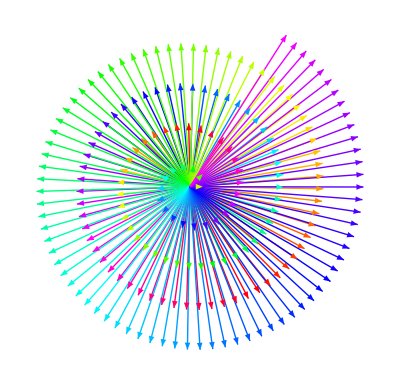

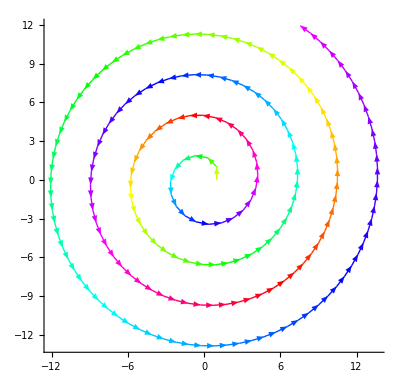

```mathematica
Graphics[ArrowT]
Graphics[ArrowEdge,Axes->True,AxesStyle->Dotted]
```

```mathematica
L=Table[n[i],{i,1,num+1}];
```

```mathematica
Le=Table[Norm[n[i]],{i,1,num+1}];
```

```mathematica
Te=Sum[N[Norm[n[i]]-√i],{i,1,num+1}]
```

1.79856×10^-13

```mathematica
Ang=Table[N[Arg[n[i][[1]]+ⅈ n[i][[2]]]],{i,1,101}];
```

```mathematica
Table[Ang[[i]]=Ang[[i]]+2π,{i,7,33}];
Table[Ang[[i]]=Ang[[i]]+2π*2,{i,34,79}];
Table[Ang[[i]]=Ang[[i]]+2π*3,{i,80,101}];
```

```mathematica
FindFit[Ang,a t^b+c ,{a,b,c,d,e},t]
```

{a→1.93746,b→0.505116,c→-1.97244,d→1.,e→1.}

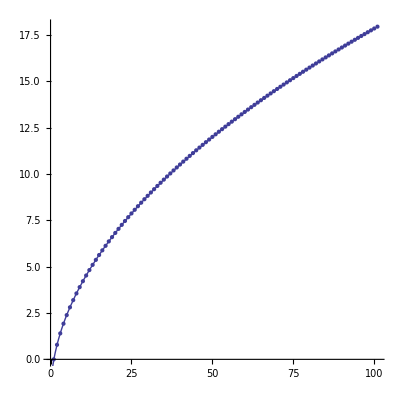

```mathematica
Show[
ListPlot[Ang,AspectRatio->1],
Plot[1.9374 t^0.505-1.97244,{t,0,100}]
]
```

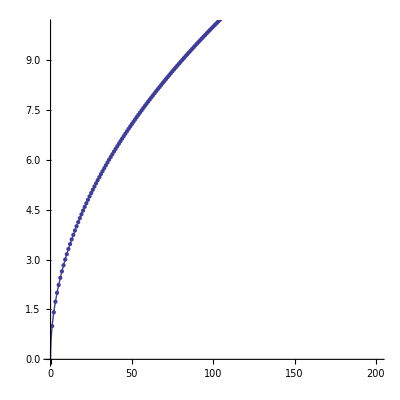

```mathematica
Show[
ListPlot[Le,PlotRange->{{0,num+1},{0,10}},AspectRatio->1],
Plot[√t,{t,0,num+1}]
]
```

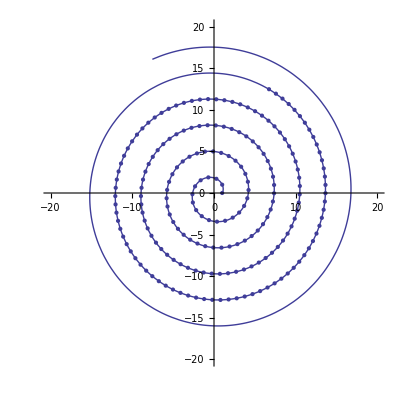

```mathematica
Show[
ListPlot[L, PlotRange->{{-20,20},{-20,20}},AspectRatio->1],
ParametricPlot[√(t+1){Cos[1.9374(t+1)^0.505-1.97244],Sin[1.9374(t+1)^0.505-1.97244]},{t,0,100π}]
]
```

```mathematica
RSolve[{
a[i+1]==a[i]-(-b[i])/(√((a[i])^2+(b[i])^2)),
b[i+1]==b[i]+a[i]/(√((a[i])^2+(b[i])^2)),
a[1]==1,b[1]==0
},{a[i],b[i]},i]
```

RSolve[{a[1+i]==a[i]+b[i]/(√(a[i]^2+b[i]^2)),b[1+i]==b[i]+a[i]/(√(a[i]^2+b[i]^2)),a[1]==1,b[1]==0},{a[i],b[i]},i]

```mathematica
(b+1/(√(1+(b/a)^2)))/(a-b/(a √(1+(b/a)^2)))//Simplify
```

(b+1/(√(1+b^2/a^2)))/(a-b/(a √(1+b^2/a^2)))

```mathematica
Tan[Subscript[ϕ, i+1]]=(1+b √(1+Tan[ϕ]^2))/(-Tan[ϕ]+a √(1+Tan[ϕ]^2))
```

```mathematica
Tan[ϕ]=b/a
```